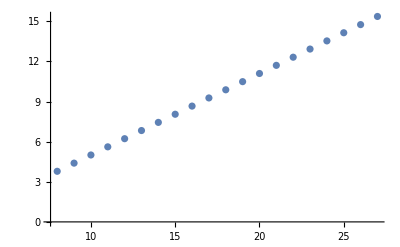

```mathematica
data={{8,44},{9,81},{10,149},{11,274},{12,504},{13,927},{14,1705},{15,3136},{16,5768},{17,10609},{18,19513},{19,35890},{20,66012},{21,121415},{22,223317},{23,410744},{24,755476},{25,1389537},{26,2555757},{27,4700770}};
logData= Transpose[{data[[;;,1]],Log[data[[;;,2]]]}];
ListPlot[logData]
```

```mathematica
logData
```

{{8,Log[44]},{9,Log[81]},{10,Log[149]},{11,Log[274]},{12,Log[504]},{13,Log[927]},{14,Log[1705]},{15,Log[3136]},{16,Log[5768]},{17,Log[10609]},{18,Log[19513]},{19,Log[35890]},{20,Log[66012]},{21,Log[121415]},{22,Log[223317]},{23,Log[410744]},{24,Log[755476]},{25,Log[1389537]},{26,Log[2555757]},{27,Log[4700770]}}

```mathematica
fit=LinearModelFit[logData,{x},{x}]
```

FittedModel[-1.0902+0.609389 x]

```mathematica
NumberForm[fit["AdjustedRSquared"], 10]
```

0.9999997396

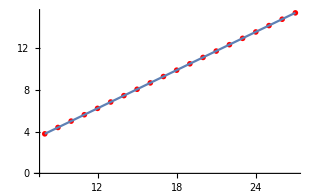

```mathematica
Show[ListPlot[logData,PlotStyle->Red],Plot[fit[x],{x,8,27}]]
```

```mathematica
IntegerPart[Exp[fit[29]]]
```

15904033